# Forest Fire

## Héctor Manuel Sánchez Castellanos

```mathematica
<<CellularAutomata`;
Fire[kernelValues_]:=Module[{tempKernelValues,midPoint},
midPoint=Floor[(kernelValues//Length)/2]+1;
(*Print[kernelValues];*)
tempKernelValues=kernelValues;
(*Burning->Burned*)
tempKernelValues=If[kernelValues[[midPoint]]==2,ReplacePart[kernelValues,3->0],tempKernelValues];
(*Green->Burning*)
tempKernelValues=If[Count[kernelValues,2]>0,ReplacePart[kernelValues,3->2],tempKernelValues];
tempKernelValues
]
```

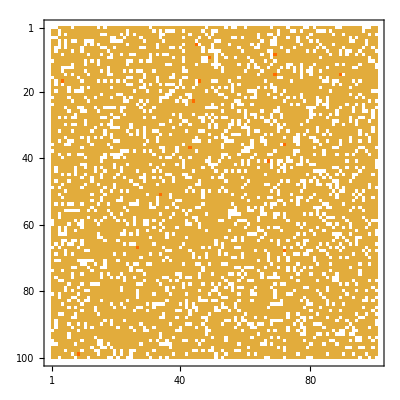

```mathematica
ca=RandomChoice[{.195,.8,.001}->{0,1,2},{100,100}];
%//MatrixPlot
```

```mathematica
kernel=CrossMatrix[1];
EvaluateCAThroughEpochs[ca,kernel,Fire,0,20,True];
frames=MatrixPlot/@%;
ListAnimate[frames]
(*Export["forestFire.gif",frames]*)
```